# Right Spherical PZX Triangle at Sunset - Fiji Waters

## When h = 0, the zenith distance ZX = 90 degrees, creating a right spherical triangle

```mathematica
(* Parameters - Fiji waters sunset *)
latitude = -18;
declination = -15.8;
(* At sunset h = 0 *)
altitude = 0;
```

```mathematica
phi = latitude Degree;
delta = declination Degree;
```

```mathematica
(* Calculate LHA at sunset (h=0) *)
(* cos(LHA) = - tan(lat) tan(dec) *)
cosLHA = -Tan[phi] Tan[delta];
```

```mathematica
LHA = ArcCos[cosLHA];
LHAdeg = LHA / Degree;
Print["LHA at sunset: ", NumberForm[LHAdeg, 4], " degrees"];
```

LHA at sunset: 95.28 degrees

```mathematica
(* Calculate azimuth at sunset (amplitude) *)
(* sin(A) = sin(dec) / cos(lat) *)
sinAz = Sin[delta] / Cos[phi];
```

```mathematica
azimuth = ArcSin[sinAz];
azDeg = azimuth / Degree;
Print["Azimuth from West: ", NumberForm[azDeg, 4], " degrees South of West"];
```

Azimuth from West: -16.64 degrees South of West

## 3D Celestial Sphere View

```mathematica
(* 3D positions on unit sphere *)
(* Coordinate system with z up (zenith), x south, y west *)
zenithPos = {0, 0, 1};
(* SCP is at altitude = -latitude in the south *)
scpAlt = -phi;
polePos = {Cos[scpAlt], 0, Sin[scpAlt]};
```

```mathematica
(* Sun position at sunset on horizon *)
(* Sun sets south of west in southern hemisphere, same name *)
sunPos = {Sin[azimuth], Cos[azimuth], 0};
```

```mathematica
(* Celestial sphere *)
sphere = ParametricPlot3D[
  {Cos[u] Cos[v], Sin[u] Cos[v], Sin[v]},
  {u, 0, 2 Pi}, {v, 0, Pi/2},
  PlotStyle -> {Opacity[0.1], LightBlue},
  Mesh -> None];
```

```mathematica
(* Horizon circle *)
horizon = ParametricPlot3D[
  {Cos[u], Sin[u], 0},
  {u, 0, 2 Pi},
  PlotStyle -> {Brown, Thickness[0.004]}];
```

```mathematica
(* Great circle arc from P to Z (colatitude) *)
pzArc = ParametricPlot3D[
  (1-t) polePos + t zenithPos,
  {t, 0, 1},
  PlotStyle -> {Blue, Thickness[0.005]}];
(* Normalize to sphere *)
pzArcNorm = ParametricPlot3D[
  Module[{pt = (1-t) polePos + t zenithPos}, pt/Norm[pt]],
  {t, 0, 1},
  PlotStyle -> {Blue, Thickness[0.005]}];
```

```mathematica
(* Great circle arc from Z to X (zenith distance = 90) *)
zxArcNorm = ParametricPlot3D[
  Module[{pt = (1-t) zenithPos + t sunPos}, pt/Norm[pt]],
  {t, 0, 1},
  PlotStyle -> {Purple, Thickness[0.005]}];
(* Great circle arc from P to X (polar distance) *)
pxArcNorm = ParametricPlot3D[
  Module[{pt = (1-t) polePos + t sunPos}, pt/Norm[pt]],
  {t, 0, 1},
  PlotStyle -> {Darker[Orange], Thickness[0.005]}];
```

```mathematica
(* Points *)
pointP = Graphics3D[{Blue, PointSize[0.03], Point[polePos]}];
pointZ = Graphics3D[{Darker[Green], PointSize[0.03], Point[zenithPos]}];
pointX = Graphics3D[{Darker[Orange], PointSize[0.035], Point[sunPos]}];
```

```mathematica
(* Right angle marker at X *)
rightAngle = Graphics3D[{Red, Thickness[0.003],
  Line[{
    sunPos + 0.08 Normalize[zenithPos - sunPos],
    sunPos + 0.08 Normalize[zenithPos - sunPos] + 0.08 Normalize[polePos - sunPos],
    sunPos + 0.08 Normalize[polePos - sunPos]
  }]}];
```

```mathematica
(* Labels *)
labels = Graphics3D[{
  Text[Style["P (SCP)", Bold, 14, Blue], polePos + {0.12, 0, -0.08}],
  Text[Style["Z (Zenith)", Bold, 14, Darker[Green]], zenithPos + {0.1, 0.1, 0.08}],
  Text[Style["X (Sun at Sunset)", Bold, 14, Darker[Orange]], sunPos + {0.05, 0.15, 0.1}],
  Text[Style["Horizon", Italic, 12, Brown], {-0.9, 0.5, 0.08}],
  (* Side labels *)
  Text[Style["PZ = 90 - lat", 11, Blue], (polePos + zenithPos)/2 + {-0.15, -0.1, 0}],
  Text[Style["ZX = 90 (Right Angle!)", Bold, 11, Purple], (zenithPos + sunPos)/2 + {0.1, 0.15, 0.05}],
  Text[Style["PX = 90 - dec", 11, Darker[Orange]], (polePos + sunPos)/2 + {0.15, 0.1, -0.05}],
  (* Angle labels *)
  Text[Style["LHA", Bold, 12, Darker[Blue]], polePos + {-0.1, 0.2, 0.15}],
  Text[Style["Az", Bold, 12, Darker[Green]], zenithPos + {0.15, 0.15, -0.1}],
  Text[Style["90 deg", Bold, 11, Red], sunPos + {-0.15, -0.1, 0.12}]
}];
```

```mathematica
(* Cardinal directions *)
cardinals = Graphics3D[{
  Text[Style["S", Bold, 14], {1.15, 0, 0}],
  Text[Style["N", Bold, 14], {-1.15, 0, 0}],
  Text[Style["W", Bold, 14], {0, 1.15, 0}],
  Text[Style["E", Bold, 14], {0, -1.15, 0}]
}];
```

```mathematica
sunsetPZX = Show[
  sphere, horizon,
  pzArcNorm, zxArcNorm, pxArcNorm,
  pointP, pointZ, pointX,
  rightAngle,
  labels, cardinals,
  PlotRange -> {{-1.3, 1.3}, {-1.3, 1.3}, {-0.3, 1.3}},
  Boxed -> False,
  Axes -> False,
  ViewPoint -> {2, 3, 1.5},
  ImageSize -> 650,
  Background -> White,
  PlotLabel -> "Right Spherical Triangle PZX at Sunset\nFiji Waters: lat = 18S, dec = 15.8S\nZX = 90 deg (sun on horizon)"
];
```

```mathematica
sunsetPZX
```

-Graphics3D-

## Horizon View (Looking West)

```mathematica
(* 2D view looking at western horizon *)
horizonView = Graphics[{
  (* Sky *)
  {RGBColor[1, 0.8, 0.6], Rectangle[{-2, 0}, {2, 2}]},
  (* Ground *)
  {RGBColor[0.3, 0.5, 0.3], Rectangle[{-2, -0.5}, {2, 0}]},
  (* Horizon *)
  {Brown, Thickness[0.005], Line[{{-2, 0}, {2, 0}}]},
  (* Sun on horizon *)
  {Orange, Disk[{azDeg/30, 0}, 0.15]},
  (* Vertical line to zenith *)
  {Purple, Dashed, Thickness[0.003], Line[{{azDeg/30, 0}, {azDeg/30, 1.8}}]},
  (* West direction *)
  {Darker[Green], Dashed, Thickness[0.002], Line[{{0, 0}, {0, 1.8}}]},
  (* Labels *)
  Text[Style["Sun", Bold, 14, Darker[Orange]], {azDeg/30 + 0.25, 0.15}],
  Text[Style["West", Bold, 12], {0, 1.9}],
  Text[Style["Zenith", Italic, 11, Purple], {azDeg/30 + 0.25, 1.7}],
  Text[Style["SW", Bold, 12], {-1.5, -0.35}],
  Text[Style["NW", Bold, 12], {1.5, -0.35}],
  (* Azimuth angle arc *)
  {Darker[Green], Thickness[0.003], Circle[{0, 0}, 0.4, {Pi/2, Pi/2 + azimuth}]},
  Text[Style["Az = " <> ToString[Round[Abs[azDeg], 0.1]] <> " deg S of W", Bold, 11, Darker[Green]], {-0.6, 0.5}],
  (* ZX = 90 label *)
  Text[Style["ZX = 90 deg\n(Right Angle)", Bold, 12, Purple], {azDeg/30 + 0.5, 0.9}]
},
PlotRange -> {{-2, 2}, {-0.5, 2.1}},
ImageSize -> 550,
Background -> White,
Axes -> False,
Frame -> False,
PlotLabel -> "Horizon View at Sunset - Looking West\nSun sets South of West (same name: both Southern)"
];
```

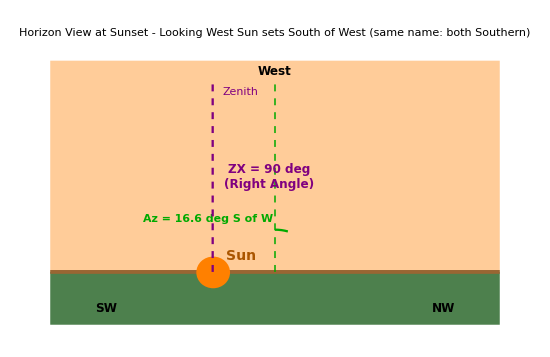

```mathematica
horizonView
```

## Triangle Summary Diagram

```mathematica
triangleSummary = Graphics[{
  {RGBColor[0.95, 0.98, 1], Rectangle[{0, 0}, {10, 8}]},
  Text[Style["Right Spherical Triangle at Sunset/Sunrise", Bold, 18], {5, 7.5}],
  (* Triangle diagram *)
  {Thickness[0.004],
   (* Sides *)
   {Blue, Line[{{2, 2}, {5, 6}}]},
   {Purple, Line[{{5, 6}, {8, 2}}]},
   {Darker[Orange], Line[{{8, 2}, {2, 2}}]}},
  (* Vertices *)
  {Blue, PointSize[0.02], Point[{2, 2}]},
  {Darker[Green], PointSize[0.02], Point[{5, 6}]},
  {Darker[Orange], PointSize[0.02], Point[{8, 2}]},
  (* Right angle marker *)
  {Red, Thickness[0.003], Line[{{8, 2.4}, {7.6, 2.4}, {7.6, 2}}]},
  (* Vertex labels *)
  Text[Style["P (Pole)", Bold, 14, Blue], {2, 1.6}],
  Text[Style["Z (Zenith)", Bold, 14, Darker[Green]], {5, 6.4}],
  Text[Style["X (Sun on Horizon)", Bold, 14, Darker[Orange]], {8, 1.6}],
  (* Side labels *)
  Text[Style["PZ = 90 - lat\n(colatitude)", 12, Blue], {2.8, 4.3}],
  Text[Style["ZX = 90 deg\n(RIGHT ANGLE)", Bold, 12, Purple], {7.2, 4.3}],
  Text[Style["PX = 90 - dec\n(polar distance)", 12, Darker[Orange]], {5, 1.5}],
  (* Angle labels *)
  Text[Style["LHA", Bold, 12, Darker[Blue]], {2.5, 2.5}],
  Text[Style["Az", Bold, 12, Darker[Green]], {5, 5.4}],
  Text[Style["90 deg", Bold, 12, Red], {8.5, 2.5}]
},
ImageSize -> 550,
Background -> White
];
```

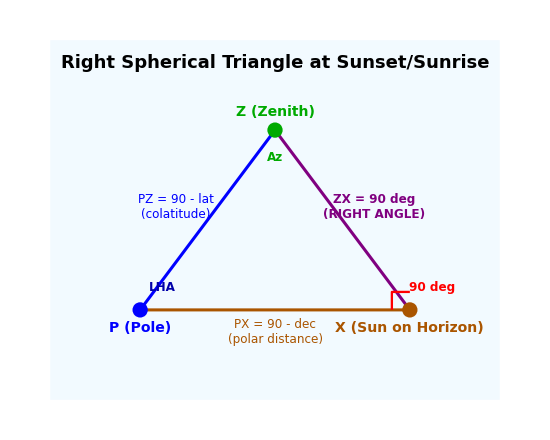

```mathematica
triangleSummary
```

## Key Equations

```mathematica
equationBox = Graphics[{
  {RGBColor[0.95, 1, 0.95], Rectangle[{0, 0}, {10, 6}]},
  {EdgeForm[{Darker[Green], Thickness[0.003]}], White, Rectangle[{0.3, 0.3}, {9.7, 5.7}]},
  Text[Style["Right Spherical Triangle Equations (h = 0)", Bold, 16, Darker[Green]], {5, 5.3}],
  Text[Style["cos(LHA) = -tan(lat) tan(dec)", 14], {5, 4.5}],
  Text[Style["sin(Az) = sin(dec) / cos(lat)", 14], {5, 3.7}],
  Text[Style["cos(PX) = cos(lat) cos(LHA)", 14], {5, 2.9}],
  Text[Style["sin(Az) = sin(LHA) cos(dec) / cos(h)", 14], {5, 2.1}],
  Text[Style["(Napier's Rules for Right Spherical Triangles)", Italic, 11], {5, 1}]
},
ImageSize -> 550,
Background -> White
];
```

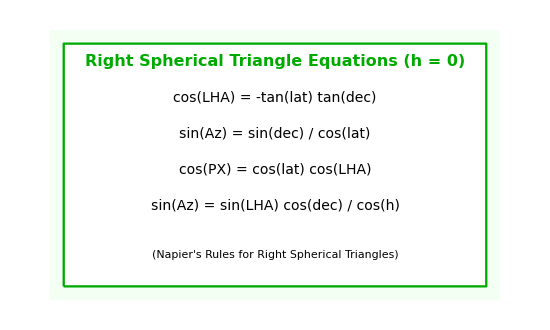

```mathematica
equationBox
```

## Export Commands

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["sunset_pzx_3d.png", sunsetPZX, ImageResolution -> 150]
```

sunset_pzx_3d.png

```mathematica
Export["sunset_horizon_view.png", horizonView, ImageResolution -> 150]
```

sunset_horizon_view.png

```mathematica
Export["sunset_triangle_summary.png", triangleSummary, ImageResolution -> 150]
```

sunset_triangle_summary.png

```mathematica
Export["sunset_equations.png", equationBox, ImageResolution -> 150]
```

sunset_equations.png